```mathematica
(* Birkhoff map for 3 disks of radius 1 with centers at the vertices of an equilateral triangle r: disk 1 centered on (0, 0), disk 2 on (r, 0) and disk 3 on (r/2, r(√3)/2) *)
```

```mathematica
(* θ is the angle of the impact point taken CCW to x-axis; φ is the angle between the incident point and the normal, w = sin φ *)
```

```mathematica
α[n_,m_]:=Which[n==1&&m==2,0,n==2&&m==3,(2π)/3,n==3&&m==1,(4π)/3,n==2&&m==1,π,n==3&&m==2,(5π)/3,n==1&&m==3,π/3]
```

```mathematica
wnext[w_,θ_,n_,m_,r_]:=w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]])
```

```mathematica
T[w_,θ_,n_,m_,r_]:={w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]]),Mod[θ+π+ArcSin[w] +ArcSin[wnext[w,θ,n,m,r]] ,2π]}
```

```mathematica
(* Limits on w and θ for the starting point on disk 1: 0≤θ≤π/3 and Subscript[w, 1]≤w≤Subscript[w, 2], where *)
```

```mathematica
w1[θ_,r_]:=Sin[θ-ArcTan[((√3)/2-Sin[θ])/(r-1-Cos[θ])]]
```

```mathematica
w2[θ_,r_]:=Sin[θ+ArcTan[Sin[θ]/(r-1-Cos[θ])]]
```

```mathematica
(* Birkhoff belt 1-2 *)
```

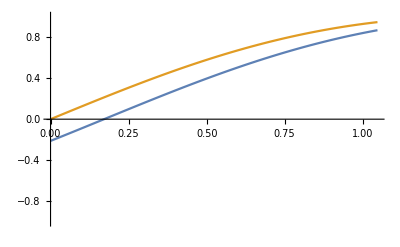

```mathematica
Plot[{w1[θ,6],w2[θ,6]},{θ,0,π/3},PlotRange->{-1,1}]
```

```mathematica
(* Reflection from two disks 1-3-1 - solution w=0,θ=π/3 *)
```

```mathematica
f1[w_,θ_]:=T[T[w,θ,1,3,3.5][[1]],T[w,θ,1,3,3.5][[2]],3,1,3.5]-{w,θ}
```

```mathematica
FindRoot[f1[w,θ],{{w,-0.1},{θ,0.4}}]
```

{w→-5.53011×10^-16+6.81025×10^-16 ⅈ,θ→1.0472-1.12441×10^-15 ⅈ}

```mathematica
-2.0943951023931953/π
```

-0.666667

```mathematica
f1[0,-2.0943951023931953]
```

{8.11483×10^-16,6.28319}

```mathematica
1.0471975511965976/π
```

0.333333

```mathematica
f1[0,1.0472]
```

{0.,-4.89761×10^-6}

```mathematica
T0[x_,n_,m_,r_]:=T[x⟦1⟧,x⟦2⟧,n,m,r]
```

```mathematica
f13[x_]:=T0[T0[x,1,3,3.5],3,1,3.5]-x
```

```mathematica
FindRoot[f13[{w,θ}]=={0,0},{{w,-0.1},{θ,0.4}}]
```

{w→-5.53011×10^-16+6.81025×10^-16 ⅈ,θ→1.0472-1.12441×10^-15 ⅈ}

```mathematica
π/3//N
```

1.0472

```mathematica
(* 123 orbit - obvious solution θ=π/6, φ=-π/6 or w=-1/2 *)
```

```mathematica
(* Larger r leads to fails in FindRoot, so it's better to keep it small, e.g. 3 *)
```

```mathematica
f123[x_]:=T0[T0[T0[x,1,2,3],2,3,3],3,1,3]-x
```

```mathematica
{w,θ}/.FindRoot[f123[{w,θ}],{{w,-0.5},{θ,0.53}}]
```

```mathematica
point0:={-0.5000000000000209,0.5235987755983147}
```

```mathematica
T0[{-0.5000000000000209,0.5235987755983147},1,2,3]
```

{-0.5,2.61799}

```mathematica
disks:=ContourPlot[{(x-0)^2+(y-0)^2==1,(x-3)^2+(y-0)^2==1,(x-1.5)^2+(y-3√3/2)^2==1,},{x,-1,4},{y,-1,4}]
```

```mathematica
BirkhoffPoint[point_,disknumber_]:=Which[disknumber==1,{Cos[point⟦2⟧],Sin[point⟦2⟧]},disknumber==2,{3+Cos[point⟦2⟧],Sin[point⟦2⟧]},disknumber==3,{1.5+Cos[point⟦2⟧],3√3/2+Sin[point⟦2⟧]}]
```

```mathematica
BirkhoffPoint[point0,1]
```

{0.866025,0.5}

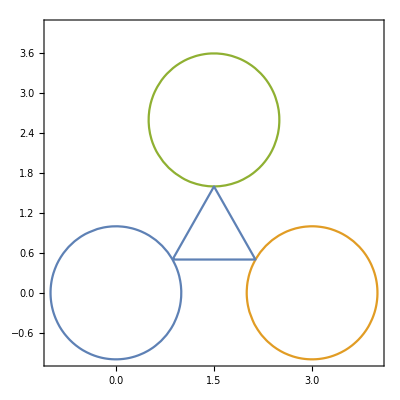

```mathematica
Show[disks,ListPlot[{BirkhoffPoint[point0,1],BirkhoffPoint[T0[point0,1,2,3],2],BirkhoffPoint[T0[T0[point0,1,2,3],2,3,3],3],BirkhoffPoint[point0,1]},Joined->True]]
```

```mathematica
%[[2]]/(π/6)
```

1.

```mathematica
(* 132 orbit - here θ=π/6,w=1/2 *)
```

```mathematica
f132[x_]:=T0[T0[T0[x,1,3,3],3,2,3],2,1,3]-x
```

```mathematica
{w,θ}/.FindRoot[f132[{w,θ}],{{w,0.5},{θ,0.5}}]
```

{0.5+8.60948×10^-14 ⅈ,0.523599-6.54618×10^-14 ⅈ}

```mathematica
(* There is an orbit 12313 (Gaspard p.183) *)
```

```mathematica
f12313[x_]:=T0[T0[T0[T0[T0[x,1,2,2.1],2,3,2.1],3,1,2.1],1,3,2.1],3,1,2.1]-x
```

```mathematica
{w,θ}/.FindRoot[f12313[{w,θ}],{{w,0.33},{θ,0.48}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{8.60847+6.8723 ⅈ,-2.36312-3.18714 ⅈ}

```mathematica
f12313[{-0.7890691835255818,0.6599239306093462}]
```

{-5.21805×10^-15,-4.55191×10^-15}

```mathematica
f12313[{0.12,0.001]
```

```mathematica
Plot[f12313[{w,1}][[1]],{w,0,.1}]
```

-Graphics-

```mathematica
{w,θ}/.FindRoot[f12313[{w,θ}],{{w,0.065},{θ,1}}]
```

{0.0947864,1.08987}

```mathematica
f12313[{0.09478642663400827,1.089869463299444}]
```

{1.18239×10^-13,1.44373×10^-12}

```mathematica
sol[w0_,θ0_]:={w,θ}/.FindRoot[f12313[{w,θ}],{{w,w0},{θ,θ0}}]
```

```mathematica
sol[0.01,0.07]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.01+6.55606×10^-16 ⅈ,0.07+1.55723×10^-15 ⅈ}

```mathematica
answers:=Quiet[Flatten[Table[sol[w0,θ0],{θ0,0,1,0.01},{w0,-1,1,0.01}],1]]
```

```mathematica
answers
```

{{-0.895906-0.0243627 ⅈ,3.32824+2.6321 ⅈ},{-0.99-2.21177×10^-16 ⅈ,9.87618×10^-16+2.06691×10^-15 ⅈ},{-0.98-2.55451×10^-16 ⅈ,1.19649×10^-15+1.95777×10^-15 ⅈ},20296,{0.99-7.19953×10^-16 ⅈ,1.+5.66464×10^-15 ⅈ},{1.00024+4.26239×10^-17 ⅈ,1.08836-0.184191 ⅈ}}
 |  |  |  |

```mathematica
Length[answers]
```

20301

```mathematica
answers1:={};For[i=1,i≤Length[answers],i++,If[Max[Im[answers[[i]][[1]]],Im[answers[[i]][[2]]]]<10^-10,AppendTo[answers1,answers[[i]]]]]
```

$Aborted

```mathematica
answersReal:=Re[answers1]
```

```mathematica
answersReal
```

{{-0.6,4.48256×10^-16},{-0.5,1.02501×10^-15},{-0.4,1.74119×10^-15},{-0.3,2.00568×10^-15},{-0.2,1.59804×10^-15},{-0.1,1.85339×10^-15},{2.06667×10^-15,1.65959×10^-15},{0.1,1.44495×10^-15},{0.2,2.43958×10^-15},{0.3,9.99497×10^-16},{0.4,8.43096×10^-16},{0.5,5.54484×10^-16},{0.6,1.97117×10^-16},{0.7,-3.28739×10^-16},{0.8,-7.14586×10^-16},{0.9,7.30114×10^-17},{1.,1.09717×10^-17},{0.26998,0.841399},{-0.924197,0.398591},{-0.7,0.1},{-0.5,0.1},{-0.4,0.1},{-0.3,0.1},{-0.2,0.1},{-0.1,0.1},{2.21022×10^-15,0.1},{0.1,0.1},{0.2,0.1},{0.3,0.1},{0.4,0.1},{0.5,0.1},{0.6,0.1},{0.7,0.1},{0.8,0.1},{0.9,0.1},{1.,0.1},{-1.,0.2},{0.11356,0.797554},{0.135784,1.26492},{-0.3,0.2},{-0.2,0.2},{-0.1,0.2},{2.36808×10^-15,0.2},{0.1,0.2},{0.2,0.2},{0.3,0.2},{0.4,0.2},{0.5,0.2},{0.6,0.2},{0.7,0.2},{0.8,0.2},{0.9,0.2},{1.,0.2},{-0.614503,0.428175},{-0.720886,0.291167},{13.393,1.18677},{-1.58434,0.796315},{-0.1,0.3},{3.7379×10^-16,0.3},{0.1,0.3},{0.2,0.3},{0.3,0.3},{0.4,0.3},{0.5,0.3},{0.6,0.3},{0.7,0.3},{0.8,0.3},{0.9,0.3},{1.,0.3},{-0.4,0.4},{-0.231197,0.646197},{-3.32813×10^-15,0.4},{0.1,0.4},{0.2,0.4},{0.3,0.4},{0.4,0.4},{0.5,0.4},{0.6,0.4},{0.7,0.4},{0.8,0.4},{0.9,0.4},{0.707702,0.981604},{-0.119764,0.787453},{-0.542622,0.473249},{-0.382136,0.55184},{0.1,0.5},{0.2,0.5},{0.3,0.5},{0.4,0.5},{0.5,0.5},{0.6,0.5},{0.7,0.5},{0.8,0.5},{0.9,0.5},{1.,0.5},{0.2,0.6},{0.3,0.6},{0.4,0.6},{0.5,0.6},{0.6,0.6},{0.7,0.6},{0.8,0.6},{0.9,0.6},{-0.9,0.7},{-0.8,0.7},{-0.7,0.7},{0.174948,0.890687},{-0.00446527,0.954849},{0.154773,0.808918},{0.2,0.7},{0.3,0.7},{0.4,0.7},{0.5,0.7},{0.6,0.7},{0.7,0.7},{0.8,0.7},{0.9,0.7},{1.,0.7},{-0.680125,0.718694},{-2.03443,0.730097},{0.283022,1.01981},{0.261493,0.906411},{0.3,0.8},{0.5,0.8},{0.6,0.8},{0.7,0.8},{0.8,0.8},{0.9,0.8},{1.,0.8},{-1.,0.9},{23.5893,0.211624},{-0.3,0.9},{0.336383,0.832404},{0.3,0.9},{0.4,0.9},{0.5,0.9},{0.6,0.9},{0.7,0.9},{0.8,0.9},{1.,0.9},{-1.,1.},{-2.83909,-0.775635},{0.249928,1.2574},{0.343151,1.0507},{0.3,1.},{0.4,1.},{0.5,1.},{0.6,1.},{0.7,1.},{0.8,1.},{1.00024,1.08836}}

```mathematica
Table[f12313[answersReal[[i]]],{i,Length[answersReal]}]
```

{{9.01947-0.0207852 ⅈ,1.04548+6.04206 ⅈ},{-5.62051-4.70586 ⅈ,2.00377+2.04551 ⅈ},{10.9913+5.16224 ⅈ,5.49046+5.15738 ⅈ},{15.47-6.27234 ⅈ,5.53721+3.51907 ⅈ},{19.6069-12.435 ⅈ,5.21333+2.37458 ⅈ},{22.674-18.3521 ⅈ,4.91588+1.55476 ⅈ},{24.2619-24.4853 ⅈ,4.60582+0.92851 ⅈ},{24.1412-30.5963 ⅈ,4.28055+0.437229 ⅈ},{22.2549-36.1943 ⅈ,3.94091+0.0513628 ⅈ},{18.775-40.6838 ⅈ,3.58785+6.03889 ⅈ},{14.1526-43.4924 ⅈ,3.22226+5.82685 ⅈ},{9.12868-44.2279 ⅈ,2.84558+5.69804 ⅈ},{4.66258-42.8731 ⅈ,2.46024+5.65698 ⅈ},{1.70479-39.9933 ⅈ,2.06854+5.71158 ⅈ},{0.669861-36.842 ⅈ,1.66007+5.87373 ⅈ},{0.291169-34.8481 ⅈ,1.15246+6.20525 ⅈ},{-4.92314-25.5348 ⅈ,6.18767+1.93567 ⅈ},{23.68-1.26377 ⅈ,-0.0154838+2.50294 ⅈ},{127.458-182.93 ⅈ,0.783156+5.20603 ⅈ},{-38.699-22.1028 ⅈ,5.07434+2.45246 ⅈ},{67.0057-3.22088 ⅈ,0.941845+5.26164 ⅈ},{22.0345+71.8655 ⅈ,4.61975+2.65992 ⅈ},{14.6045+2.01334 ⅈ,6.01102+5.04664 ⅈ},{17.5517-6.10248 ⅈ,5.70241+3.24527 ⅈ},{21.6753-11.8363 ⅈ,5.36735+2.1879 ⅈ},{25.1184-17.9552 ⅈ,5.04905+1.37369 ⅈ},{27.1234-24.8021 ⅈ,4.71156+0.723313 ⅈ},{27.0994-32.0804 ⅈ,4.34753+0.197274 ⅈ},{24.6363-39.0446 ⅈ,3.95463+6.06068 ⅈ},{19.7217-44.5827 ⅈ,3.53191+5.74212 ⅈ},{13.0257-47.4391 ⅈ,3.07998+5.52987 ⅈ},{6.10076-46.7153 ⅈ,2.60306+5.43852 ⅈ},{1.16995-42.6919 ⅈ,2.11234+5.49021 ⅈ},{-0.117985-37.6489 ⅈ,1.61659+5.7048 ⅈ},{0.200478-34.9542 ⅈ,1.01454+6.14497 ⅈ},{-2.62513-21.2738 ⅈ,6.1009+2.90257 ⅈ},{10.5552-14.9902 ⅈ,2.34537+4.33508 ⅈ},{-1827.34-2340.92 ⅈ,5.20891+0.357757 ⅈ},{-6674.56-10678.2 ⅈ,-0.227033+5.18603 ⅈ},{57.2012+39.0479 ⅈ,5.87314+2.43196 ⅈ},{16.8724+1.55373 ⅈ,-0.0292456+5.13876 ⅈ},{18.9941-5.20005 ⅈ,5.89415+3.11783 ⅈ},{23.5191-10.9375 ⅈ,5.51685+2.03974 ⅈ},{27.6302-17.7269 ⅈ,5.14937+1.17514 ⅈ},{30.0742-25.9226 ⅈ,4.75219+0.469495 ⅈ},{29.6823-35.0569 ⅈ,4.31308+6.17859 ⅈ},{25.5319-43.735 ⅈ,3.82661+5.72929 ⅈ},{17.6485-49.6583 ⅈ,3.291+5.41429 ⅈ},{7.94138-50.3698 ⅈ,2.71087+5.25956 ⅈ},{0.477413-45.2271 ⅈ,2.10699+5.30686 ⅈ},{-0.957434-37.9854 ⅈ,1.51775+5.58882 ⅈ},{0.00997216-34.9244 ⅈ,0.813992+6.1624 ⅈ},{4.78095-20.7577 ⅈ,0.561445+3.9565 ⅈ},{-99.854+195.351 ⅈ,2.8057+4.79134 ⅈ},{1.1646,1.01147},{34.3138-8.60289 ⅈ,0.0835852+5.06931 ⅈ},{1371.93-157.322 ⅈ,3.16382+1.89397 ⅈ},{18.52+1.26753 ⅈ,0.193232+5.25933 ⅈ},{20.2278-4.38928 ⅈ,-0.233182+2.98628 ⅈ},{25.6157-10.585 ⅈ,5.60128+1.81868 ⅈ},{30.5923-18.8232 ⅈ,5.1511+0.869954 ⅈ},{33.0295-29.4201 ⅈ,4.6546+0.0984162 ⅈ},{30.7279-41.1958 ⅈ,4.09493+5.77187 ⅈ},{22.3511-50.8547 ⅈ,3.46557+5.33512 ⅈ},{9.71726-53.6397 ⅈ,2.77111+5.1091 ⅈ},{-0.551644-47.2037 ⅈ,2.04445+5.15911 ⅈ},{-1.58322-37.6805 ⅈ,1.36557+5.52895 ⅈ},{-0.492767-34.789 ⅈ,0.543537+6.27335 ⅈ},{-15.2083-119.988 ⅈ,0.906078+5.30247 ⅈ},{-83.0299-101.939 ⅈ,5.56412+0.324074 ⅈ},{2.27949,0.836038+4.93878 ⅈ},{19.0694+0.479767 ⅈ,0.382243+5.20432 ⅈ},{21.9457-4.36842 ⅈ,-0.188708+2.69099 ⅈ},{28.8157-11.9371 ⅈ,5.5452+1.40143 ⅈ},{34.3847-23.1506 ⅈ,4.9718+0.371046 ⅈ},{34.7946-37.6636 ⅈ,4.32566+5.84826 ⅈ},{26.5467-51.4246 ⅈ,3.59007+5.27255 ⅈ},{10.8249-56.5289 ⅈ,2.7697+4.97553 ⅈ},{-2.09054-48.1957 ⅈ,1.91596+5.04857 ⅈ},{-1.68376-36.7777 ⅈ,1.16412+5.53079 ⅈ},{-1.70589-34.237 ⅈ,0.193489+0.232253 ⅈ},{0.52259-35.1214 ⅈ,-0.00283567+5.79402 ⅈ},{-43.3597-3.48448 ⅈ,0.263462+5.233 ⅈ},{-0.175575,2.30722},{1.51527,1.54845+5.77273 ⅈ},{19.0006-0.175474 ⅈ,0.385263+3.80674 ⅈ},{25.4973-6.0933 ⅈ,-0.340814+2.06619 ⅈ},{34.0294-17.1842 ⅈ,5.25786+0.691902 ⅈ},{37.6689-33.9951 ⅈ,4.50741+5.9321 ⅈ},{29.8283-52.0208 ⅈ,3.65064+5.20548 ⅈ},{10.6411-59.0868 ⅈ,2.69276+4.85004 ⅈ},{-4.07193-47.7406 ⅈ,1.716+4.98325 ⅈ},{-1.06153-35.689 ⅈ,0.917055+5.59827 ⅈ},{-3.73116-32.3582 ⅈ,-0.233368+0.677812 ⅈ},{-10.5413-4.24649 ⅈ,4.28446+4.97901 ⅈ},{21.7523-1.77373 ⅈ,0.0725099+2.85816 ⅈ},{32.6017-12.1463 ⅈ,5.50513+1.03086 ⅈ},{39.6478-30.988 ⅈ,4.62776+5.99276 ⅈ},{31.9068-53.3625 ⅈ,3.63298+5.11439 ⅈ},{8.60038-61.1522 ⅈ,2.5277+4.73063 ⅈ},{-5.94594-45.4666 ⅈ,1.447+4.97933 ⅈ},{-0.0467519-35.0976 ⅈ,0.615341+5.73555 ⅈ},{-5.4206-28.0534 ⅈ,5.6007+1.44643 ⅈ},{28.0443-5.07548 ⅈ,3.15494+3.35934 ⅈ},{27.6769-4.64871 ⅈ,3.18023+3.3806 ⅈ},{29.8095-0.752372 ⅈ,3.44171+3.25893 ⅈ},{-5783.44-5159.07 ⅈ,4.75565+4.72138 ⅈ},{2261.7+1393.79 ⅈ,5.27307+3.48858 ⅈ},{-6641.9-5187.45 ⅈ,4.70663+4.55371 ⅈ},{-54.5932-5.69363 ⅈ,3.70405+2.32243 ⅈ},{30.849-8.32738 ⅈ,-0.580642+1.34558 ⅈ},{41.2021-29.3155 ⅈ,4.67241+5.99715 ⅈ},{32.4145-56.0623 ⅈ,3.52223+4.98534 ⅈ},{4.36419-62.0718 ⅈ,2.26484+4.62647 ⅈ},{-6.62151-41.5182 ⅈ,1.12564+5.05817 ⅈ},{0.172472-35.2465 ⅈ,0.226213+5.97243 ⅈ},{-3.58075-21.7529 ⅈ,5.38374+2.70953 ⅈ},{-213.705-13.1999 ⅈ,0.498068+2.16143 ⅈ},{26.7522-4.85206 ⅈ,3.14037+3.43135 ⅈ},{1707.28-186.96 ⅈ,3.24027+1.45715 ⅈ},{26.2437-1.75461 ⅈ,-0.228884+2.09067 ⅈ},{-94.8993-2.48565 ⅈ,3.33757+1.17458 ⅈ},{29.4643-5.78786 ⅈ,-0.450439+1.5793 ⅈ},{30.6581-60.3908 ⅈ,3.30356+4.81524 ⅈ},{-1.72866-60.5736 ⅈ,1.90083+4.56198 ⅈ},{-5.0377-37.1623 ⅈ,0.784739+5.22951 ⅈ},{-1.72553-34.8211 ⅈ,-0.279032+0.118306 ⅈ},{5.7484-21.1837 ⅈ,0.110725+4.06323 ⅈ},{367.057-331.469 ⅈ,1.88633+4.00816 ⅈ},{26.3084-7.58551 ⅈ,2.76666+3.44648 ⅈ},{-3913.97-3190.13 ⅈ,2.48414+2.03788 ⅈ},{-20.0061-22.3961 ⅈ,0.205516+5.24255 ⅈ},{35.7991-12.1147 ⅈ,5.39712+0.757289 ⅈ},{29.0449-4.51063 ⅈ,-0.412263+1.66376 ⅈ},{44.4853-32.5516 ⅈ,4.46714+5.72202 ⅈ},{25.4972-65.8169 ⅈ,2.96379+4.6177 ⅈ},{-7.93783-55.2637 ⅈ,1.44594+4.57925 ⅈ},{-1.64183-34.6572 ⅈ,0.436319+5.46601 ⅈ},{-4.95609-31.1679 ⅈ,-0.862612+0.899347 ⅈ},{-22.8287-94.525 ⅈ,-0.530658+1.02275 ⅈ},{9.20971-14.4035 ⅈ,1.50742+4.47269 ⅈ},{622199.-635383. ⅈ,3.35434+1.54921 ⅈ},{25.6018-0.341676 ⅈ,-0.262504+2.20419 ⅈ},{42.1458-18.3239 ⅈ,4.95256+0.0941695 ⅈ},{30.1554-4.59133 ⅈ,-0.494786+1.53225 ⅈ},{45.815-39.0443 ⅈ,4.18035+5.41891 ⅈ},{15.7968-70.2641 ⅈ,2.49479+4.42832 ⅈ},{-10.9376-46.285 ⅈ,0.939349+4.73244 ⅈ},{0.53847-35.0607 ⅈ,-0.00459333+5.76998 ⅈ},{-5.03661-23.5517 ⅈ,4.98865+2.26171 ⅈ},{-39445.4+43711.1 ⅈ,1.62157+3.41292 ⅈ}}

```mathematica
point50:={-0.7890691835255818,0.6599239306093462}
```

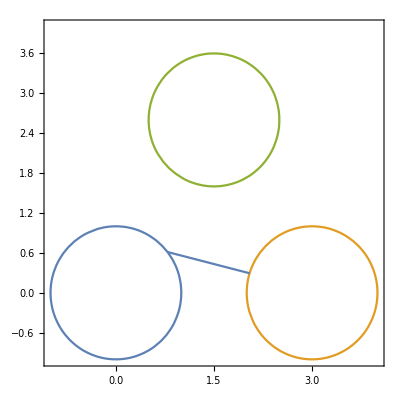

```mathematica
Show[disks,ListPlot[{BirkhoffPoint[point50,1],BirkhoffPoint[T0[point50,1,2,3],2],BirkhoffPoint[T0[T0[point50,1,2,3],2,3,3],3],BirkhoffPoint[point0,1]},Joined->True]]
```

```mathematica
T0[point50,1,2,3]
```

{-0.0486935,2.84351}

```mathematica
Plot3D[f12313[{x,y}],{x,-1,1},{y,-0.1,1}]
```

-Graphics3D-

```mathematica
f120[x_]:=T0[x,1,2,2.1]
```

```mathematica
f120[{0.4, 0.5}]
```

{-1.25991,2.48231+0.706219 ⅈ}

```mathematica
a:={-1.2599109567023814,2.4823131728623844+0.7062190210174033 ⅈ}
```

```mathematica
Max[Im[a]]
```

0.706219

```mathematica
IsReal[x_]:=Max[Im[x]]<10^-14
```

```mathematica
IsReal[a]
```

False

```mathematica
IsReal[{2, 3.2}]
```

True

```mathematica
points=Flatten[Table[{{-1+(2/30)i,(π/3)/30 j},IsReal[f120[{-1+(2/30)i,(π/3)/30 j}]]},{i,1,30},{j,1,30}],1]
```

{{{-14/15,π/90},True},{{-14/15,π/45},True},{{-14/15,π/30},True},{{-14/15,(2 π)/45},True},{{-14/15,π/18},True},{{-14/15,π/15},True},{{-14/15,(7 π)/90},True},{{-14/15,(4 π)/45},True},{{-14/15,π/10},True},{{-14/15,π/9},True},{{-14/15,(11 π)/90},True},{{-14/15,(2 π)/15},True},{{-14/15,(13 π)/90},True},{{-14/15,(7 π)/45},True},{{-14/15,π/6},True},{{-14/15,(8 π)/45},True},{{-14/15,(17 π)/90},True},{{-14/15,π/5},True},{{-14/15,(19 π)/90},True},{{-14/15,(2 π)/9},True},{{-14/15,(7 π)/30},True},{{-14/15,(11 π)/45},True},{{-14/15,(23 π)/90},True},{{-14/15,(4 π)/15},True},{{-14/15,(5 π)/18},True},{{-14/15,(13 π)/45},True},{{-14/15,(3 π)/10},True},{{-14/15,(14 π)/45},True},{{-14/15,(29 π)/90},True},{{-14/15,π/3},True},{{-13/15,π/90},True},{{-13/15,π/45},True},{{-13/15,π/30},True},{{-13/15,(2 π)/45},True},{{-13/15,π/18},True},{{-13/15,π/15},True},{{-13/15,(7 π)/90},True},{{-13/15,(4 π)/45},True},{{-13/15,π/10},True},{{-13/15,π/9},True},{{-13/15,(11 π)/90},True},{{-13/15,(2 π)/15},True},{{-13/15,(13 π)/90},True},{{-13/15,(7 π)/45},True},{{-13/15,π/6},True},{{-13/15,(8 π)/45},True},{{-13/15,(17 π)/90},True},{{-13/15,π/5},True},{{-13/15,(19 π)/90},True},{{-13/15,(2 π)/9},True},{{-13/15,(7 π)/30},True},{{-13/15,(11 π)/45},True},{{-13/15,(23 π)/90},True},{{-13/15,(4 π)/15},True},{{-13/15,(5 π)/18},True},{{-13/15,(13 π)/45},True},{{-13/15,(3 π)/10},True},{{-13/15,(14 π)/45},True},{{-13/15,(29 π)/90},True},{{-13/15,π/3},True},{{-4/5,π/90},True},{{-4/5,π/45},True},{{-4/5,π/30},True},{{-4/5,(2 π)/45},True},{{-4/5,π/18},True},{{-4/5,π/15},True},{{-4/5,(7 π)/90},True},{{-4/5,(4 π)/45},True},{{-4/5,π/10},True},{{-4/5,π/9},True},{{-4/5,(11 π)/90},True},{{-4/5,(2 π)/15},True},{{-4/5,(13 π)/90},True},{{-4/5,(7 π)/45},True},{{-4/5,π/6},True},{{-4/5,(8 π)/45},True},{{-4/5,(17 π)/90},True},{{-4/5,π/5},True},{{-4/5,(19 π)/90},True},{{-4/5,(2 π)/9},True},{{-4/5,(7 π)/30},True},{{-4/5,(11 π)/45},True},{{-4/5,(23 π)/90},True},{{-4/5,(4 π)/15},True},{{-4/5,(5 π)/18},True},{{-4/5,(13 π)/45},True},{{-4/5,(3 π)/10},True},{{-4/5,(14 π)/45},True},{{-4/5,(29 π)/90},True},{{-4/5,π/3},False},{{-11/15,π/90},True},{{-11/15,π/45},True},{{-11/15,π/30},True},{{-11/15,(2 π)/45},True},{{-11/15,π/18},True},{{-11/15,π/15},True},{{-11/15,(7 π)/90},True},{{-11/15,(4 π)/45},True},{{-11/15,π/10},True},{{-11/15,π/9},True},{{-11/15,(11 π)/90},True},{{-11/15,(2 π)/15},True},{{-11/15,(13 π)/90},True},{{-11/15,(7 π)/45},True},{{-11/15,π/6},True},{{-11/15,(8 π)/45},True},{{-11/15,(17 π)/90},True},{{-11/15,π/5},True},{{-11/15,(19 π)/90},True},{{-11/15,(2 π)/9},True},{{-11/15,(7 π)/30},True},{{-11/15,(11 π)/45},True},{{-11/15,(23 π)/90},True},{{-11/15,(4 π)/15},True},{{-11/15,(5 π)/18},True},{{-11/15,(13 π)/45},True},{{-11/15,(3 π)/10},True},{{-11/15,(14 π)/45},False},{{-11/15,(29 π)/90},False},{{-11/15,π/3},False},{{-2/3,π/90},True},{{-2/3,π/45},True},{{-2/3,π/30},True},{{-2/3,(2 π)/45},True},{{-2/3,π/18},True},{{-2/3,π/15},True},{{-2/3,(7 π)/90},True},{{-2/3,(4 π)/45},True},{{-2/3,π/10},True},{{-2/3,π/9},True},{{-2/3,(11 π)/90},True},{{-2/3,(2 π)/15},True},{{-2/3,(13 π)/90},True},{{-2/3,(7 π)/45},True},{{-2/3,π/6},True},{{-2/3,(8 π)/45},True},{{-2/3,(17 π)/90},True},{{-2/3,π/5},True},{{-2/3,(19 π)/90},True},{{-2/3,(2 π)/9},True},{{-2/3,(7 π)/30},True},{{-2/3,(11 π)/45},True},{{-2/3,(23 π)/90},True},{{-2/3,(4 π)/15},True},{{-2/3,(5 π)/18},True},{{-2/3,(13 π)/45},False},{{-2/3,(3 π)/10},False},{{-2/3,(14 π)/45},False},{{-2/3,(29 π)/90},False},{{-2/3,π/3},False},{{-3/5,π/90},True},{{-3/5,π/45},True},{{-3/5,π/30},True},{{-3/5,(2 π)/45},True},{{-3/5,π/18},True},{{-3/5,π/15},True},{{-3/5,(7 π)/90},True},{{-3/5,(4 π)/45},True},{{-3/5,π/10},True},{{-3/5,π/9},True},{{-3/5,(11 π)/90},True},{{-3/5,(2 π)/15},True},{{-3/5,(13 π)/90},True},{{-3/5,(7 π)/45},True},{{-3/5,π/6},True},{{-3/5,(8 π)/45},True},{{-3/5,(17 π)/90},True},{{-3/5,π/5},True},{{-3/5,(19 π)/90},True},{{-3/5,(2 π)/9},True},{{-3/5,(7 π)/30},True},{{-3/5,(11 π)/45},True},{{-3/5,(23 π)/90},True},{{-3/5,(4 π)/15},False},{{-3/5,(5 π)/18},False},{{-3/5,(13 π)/45},False},{{-3/5,(3 π)/10},False},{{-3/5,(14 π)/45},False},{{-3/5,(29 π)/90},False},{{-3/5,π/3},False},{{-8/15,π/90},True},{{-8/15,π/45},True},{{-8/15,π/30},True},{{-8/15,(2 π)/45},True},{{-8/15,π/18},True},{{-8/15,π/15},True},{{-8/15,(7 π)/90},True},{{-8/15,(4 π)/45},True},{{-8/15,π/10},True},{{-8/15,π/9},True},{{-8/15,(11 π)/90},True},{{-8/15,(2 π)/15},True},{{-8/15,(13 π)/90},True},{{-8/15,(7 π)/45},True},{{-8/15,π/6},True},{{-8/15,(8 π)/45},True},{{-8/15,(17 π)/90},True},{{-8/15,π/5},True},{{-8/15,(19 π)/90},True},{{-8/15,(2 π)/9},True},{{-8/15,(7 π)/30},True},{{-8/15,(11 π)/45},True},{{-8/15,(23 π)/90},False},{{-8/15,(4 π)/15},False},{{-8/15,(5 π)/18},False},{{-8/15,(13 π)/45},False},{{-8/15,(3 π)/10},False},{{-8/15,(14 π)/45},False},{{-8/15,(29 π)/90},False},{{-8/15,π/3},False},{{-7/15,π/90},True},{{-7/15,π/45},True},{{-7/15,π/30},True},{{-7/15,(2 π)/45},True},{{-7/15,π/18},True},{{-7/15,π/15},True},{{-7/15,(7 π)/90},True},{{-7/15,(4 π)/45},True},{{-7/15,π/10},True},{{-7/15,π/9},True},{{-7/15,(11 π)/90},True},{{-7/15,(2 π)/15},True},{{-7/15,(13 π)/90},True},{{-7/15,(7 π)/45},True},{{-7/15,π/6},True},{{-7/15,(8 π)/45},True},{{-7/15,(17 π)/90},True},{{-7/15,π/5},True},{{-7/15,(19 π)/90},True},{{-7/15,(2 π)/9},True},{{-7/15,(7 π)/30},True},{{-7/15,(11 π)/45},False},{{-7/15,(23 π)/90},False},{{-7/15,(4 π)/15},False},{{-7/15,(5 π)/18},False},{{-7/15,(13 π)/45},False},{{-7/15,(3 π)/10},False},{{-7/15,(14 π)/45},False},{{-7/15,(29 π)/90},False},{{-7/15,π/3},False},{{-2/5,π/90},True},{{-2/5,π/45},True},{{-2/5,π/30},True},{{-2/5,(2 π)/45},True},{{-2/5,π/18},True},{{-2/5,π/15},True},{{-2/5,(7 π)/90},True},{{-2/5,(4 π)/45},True},{{-2/5,π/10},True},{{-2/5,π/9},True},{{-2/5,(11 π)/90},True},{{-2/5,(2 π)/15},True},{{-2/5,(13 π)/90},True},{{-2/5,(7 π)/45},True},{{-2/5,π/6},True},{{-2/5,(8 π)/45},True},{{-2/5,(17 π)/90},True},{{-2/5,π/5},True},{{-2/5,(19 π)/90},True},{{-2/5,(2 π)/9},True},{{-2/5,(7 π)/30},False},{{-2/5,(11 π)/45},False},{{-2/5,(23 π)/90},False},{{-2/5,(4 π)/15},False},{{-2/5,(5 π)/18},False},{{-2/5,(13 π)/45},False},{{-2/5,(3 π)/10},False},{{-2/5,(14 π)/45},False},{{-2/5,(29 π)/90},False},{{-2/5,π/3},False},{{-1/3,π/90},True},{{-1/3,π/45},True},{{-1/3,π/30},True},{{-1/3,(2 π)/45},True},{{-1/3,π/18},True},{{-1/3,π/15},True},{{-1/3,(7 π)/90},True},{{-1/3,(4 π)/45},True},{{-1/3,π/10},True},{{-1/3,π/9},True},{{-1/3,(11 π)/90},True},{{-1/3,(2 π)/15},True},{{-1/3,(13 π)/90},True},{{-1/3,(7 π)/45},True},{{-1/3,π/6},True},{{-1/3,(8 π)/45},True},{{-1/3,(17 π)/90},True},{{-1/3,π/5},True},{{-1/3,(19 π)/90},False},{{-1/3,(2 π)/9},False},{{-1/3,(7 π)/30},False},{{-1/3,(11 π)/45},False},{{-1/3,(23 π)/90},False},{{-1/3,(4 π)/15},False},{{-1/3,(5 π)/18},False},{{-1/3,(13 π)/45},False},{{-1/3,(3 π)/10},False},{{-1/3,(14 π)/45},False},{{-1/3,(29 π)/90},False},{{-1/3,π/3},False},{{-4/15,π/90},True},{{-4/15,π/45},True},{{-4/15,π/30},True},{{-4/15,(2 π)/45},True},{{-4/15,π/18},True},{{-4/15,π/15},True},{{-4/15,(7 π)/90},True},{{-4/15,(4 π)/45},True},{{-4/15,π/10},True},{{-4/15,π/9},True},{{-4/15,(11 π)/90},True},{{-4/15,(2 π)/15},True},{{-4/15,(13 π)/90},True},{{-4/15,(7 π)/45},True},{{-4/15,π/6},True},{{-4/15,(8 π)/45},True},{{-4/15,(17 π)/90},True},{{-4/15,π/5},False},{{-4/15,(19 π)/90},False},{{-4/15,(2 π)/9},False},{{-4/15,(7 π)/30},False},{{-4/15,(11 π)/45},False},{{-4/15,(23 π)/90},False},{{-4/15,(4 π)/15},False},{{-4/15,(5 π)/18},False},{{-4/15,(13 π)/45},False},{{-4/15,(3 π)/10},False},{{-4/15,(14 π)/45},False},{{-4/15,(29 π)/90},False},{{-4/15,π/3},False},{{-1/5,π/90},True},{{-1/5,π/45},True},{{-1/5,π/30},True},{{-1/5,(2 π)/45},True},{{-1/5,π/18},True},{{-1/5,π/15},True},{{-1/5,(7 π)/90},True},{{-1/5,(4 π)/45},True},{{-1/5,π/10},True},{{-1/5,π/9},True},{{-1/5,(11 π)/90},True},{{-1/5,(2 π)/15},True},{{-1/5,(13 π)/90},True},{{-1/5,(7 π)/45},True},{{-1/5,π/6},True},{{-1/5,(8 π)/45},True},{{-1/5,(17 π)/90},False},{{-1/5,π/5},False},{{-1/5,(19 π)/90},False},{{-1/5,(2 π)/9},False},{{-1/5,(7 π)/30},False},{{-1/5,(11 π)/45},False},{{-1/5,(23 π)/90},False},{{-1/5,(4 π)/15},False},{{-1/5,(5 π)/18},False},{{-1/5,(13 π)/45},False},{{-1/5,(3 π)/10},False},{{-1/5,(14 π)/45},False},{{-1/5,(29 π)/90},False},{{-1/5,π/3},False},{{-2/15,π/90},True},{{-2/15,π/45},True},{{-2/15,π/30},True},{{-2/15,(2 π)/45},True},{{-2/15,π/18},True},{{-2/15,π/15},True},{{-2/15,(7 π)/90},True},{{-2/15,(4 π)/45},True},{{-2/15,π/10},True},{{-2/15,π/9},True},{{-2/15,(11 π)/90},True},{{-2/15,(2 π)/15},True},{{-2/15,(13 π)/90},True},{{-2/15,(7 π)/45},True},{{-2/15,π/6},True},{{-2/15,(8 π)/45},True},{{-2/15,(17 π)/90},False},{{-2/15,π/5},False},{{-2/15,(19 π)/90},False},{{-2/15,(2 π)/9},False},{{-2/15,(7 π)/30},False},{{-2/15,(11 π)/45},False},{{-2/15,(23 π)/90},False},{{-2/15,(4 π)/15},False},{{-2/15,(5 π)/18},False},{{-2/15,(13 π)/45},False},{{-2/15,(3 π)/10},False},{{-2/15,(14 π)/45},False},{{-2/15,(29 π)/90},False},{{-2/15,π/3},False},{{-1/15,π/90},True},{{-1/15,π/45},True},{{-1/15,π/30},True},{{-1/15,(2 π)/45},True},{{-1/15,π/18},True},{{-1/15,π/15},True},{{-1/15,(7 π)/90},True},{{-1/15,(4 π)/45},True},{{-1/15,π/10},True},{{-1/15,π/9},True},{{-1/15,(11 π)/90},True},{{-1/15,(2 π)/15},True},{{-1/15,(13 π)/90},True},{{-1/15,(7 π)/45},True},{{-1/15,π/6},True},{{-1/15,(8 π)/45},False},{{-1/15,(17 π)/90},False},{{-1/15,π/5},False},{{-1/15,(19 π)/90},False},{{-1/15,(2 π)/9},False},{{-1/15,(7 π)/30},False},{{-1/15,(11 π)/45},False},{{-1/15,(23 π)/90},False},{{-1/15,(4 π)/15},False},{{-1/15,(5 π)/18},False},{{-1/15,(13 π)/45},False},{{-1/15,(3 π)/10},False},{{-1/15,(14 π)/45},False},{{-1/15,(29 π)/90},False},{{-1/15,π/3},False},{{0,π/90},True},{{0,π/45},True},{{0,π/30},True},{{0,(2 π)/45},True},{{0,π/18},True},{{0,π/15},True},{{0,(7 π)/90},True},{{0,(4 π)/45},True},{{0,π/10},True},{{0,π/9},True},{{0,(11 π)/90},True},{{0,(2 π)/15},True},{{0,(13 π)/90},True},{{0,(7 π)/45},True},{{0,π/6},False},{{0,(8 π)/45},False},{{0,(17 π)/90},False},{{0,π/5},False},{{0,(19 π)/90},False},{{0,(2 π)/9},False},{{0,(7 π)/30},False},{{0,(11 π)/45},False},{{0,(23 π)/90},False},{{0,(4 π)/15},False},{{0,(5 π)/18},False},{{0,(13 π)/45},False},{{0,(3 π)/10},False},{{0,(14 π)/45},False},{{0,(29 π)/90},False},{{0,π/3},False},{{1/15,π/90},True},{{1/15,π/45},True},{{1/15,π/30},True},{{1/15,(2 π)/45},True},{{1/15,π/18},True},{{1/15,π/15},True},{{1/15,(7 π)/90},True},{{1/15,(4 π)/45},True},{{1/15,π/10},True},{{1/15,π/9},True},{{1/15,(11 π)/90},True},{{1/15,(2 π)/15},True},{{1/15,(13 π)/90},True},{{1/15,(7 π)/45},False},{{1/15,π/6},False},{{1/15,(8 π)/45},False},{{1/15,(17 π)/90},False},{{1/15,π/5},False},{{1/15,(19 π)/90},False},{{1/15,(2 π)/9},False},{{1/15,(7 π)/30},False},{{1/15,(11 π)/45},False},{{1/15,(23 π)/90},False},{{1/15,(4 π)/15},False},{{1/15,(5 π)/18},False},{{1/15,(13 π)/45},False},{{1/15,(3 π)/10},False},{{1/15,(14 π)/45},False},{{1/15,(29 π)/90},False},{{1/15,π/3},False},{{2/15,π/90},True},{{2/15,π/45},True},{{2/15,π/30},True},{{2/15,(2 π)/45},True},{{2/15,π/18},True},{{2/15,π/15},True},{{2/15,(7 π)/90},True},{{2/15,(4 π)/45},True},{{2/15,π/10},True},{{2/15,π/9},True},{{2/15,(11 π)/90},True},{{2/15,(2 π)/15},True},{{2/15,(13 π)/90},False},{{2/15,(7 π)/45},False},{{2/15,π/6},False},{{2/15,(8 π)/45},False},{{2/15,(17 π)/90},False},{{2/15,π/5},False},{{2/15,(19 π)/90},False},{{2/15,(2 π)/9},False},{{2/15,(7 π)/30},False},{{2/15,(11 π)/45},False},{{2/15,(23 π)/90},False},{{2/15,(4 π)/15},False},{{2/15,(5 π)/18},False},{{2/15,(13 π)/45},False},{{2/15,(3 π)/10},False},{{2/15,(14 π)/45},False},{{2/15,(29 π)/90},False},{{2/15,π/3},False},{{1/5,π/90},True},{{1/5,π/45},True},{{1/5,π/30},True},{{1/5,(2 π)/45},True},{{1/5,π/18},True},{{1/5,π/15},True},{{1/5,(7 π)/90},True},{{1/5,(4 π)/45},True},{{1/5,π/10},True},{{1/5,π/9},True},{{1/5,(11 π)/90},True},{{1/5,(2 π)/15},False},{{1/5,(13 π)/90},False},{{1/5,(7 π)/45},False},{{1/5,π/6},False},{{1/5,(8 π)/45},False},{{1/5,(17 π)/90},False},{{1/5,π/5},False},{{1/5,(19 π)/90},False},{{1/5,(2 π)/9},False},{{1/5,(7 π)/30},False},{{1/5,(11 π)/45},False},{{1/5,(23 π)/90},False},{{1/5,(4 π)/15},False},{{1/5,(5 π)/18},False},{{1/5,(13 π)/45},False},{{1/5,(3 π)/10},False},{{1/5,(14 π)/45},False},{{1/5,(29 π)/90},False},{{1/5,π/3},False},{{4/15,π/90},True},{{4/15,π/45},True},{{4/15,π/30},True},{{4/15,(2 π)/45},True},{{4/15,π/18},True},{{4/15,π/15},True},{{4/15,(7 π)/90},True},{{4/15,(4 π)/45},True},{{4/15,π/10},True},{{4/15,π/9},True},{{4/15,(11 π)/90},False},{{4/15,(2 π)/15},False},{{4/15,(13 π)/90},False},{{4/15,(7 π)/45},False},{{4/15,π/6},False},{{4/15,(8 π)/45},False},{{4/15,(17 π)/90},False},{{4/15,π/5},False},{{4/15,(19 π)/90},False},{{4/15,(2 π)/9},False},{{4/15,(7 π)/30},False},{{4/15,(11 π)/45},False},{{4/15,(23 π)/90},False},{{4/15,(4 π)/15},False},{{4/15,(5 π)/18},False},{{4/15,(13 π)/45},False},{{4/15,(3 π)/10},False},{{4/15,(14 π)/45},False},{{4/15,(29 π)/90},False},{{4/15,π/3},False},{{1/3,π/90},True},{{1/3,π/45},True},{{1/3,π/30},True},{{1/3,(2 π)/45},True},{{1/3,π/18},True},{{1/3,π/15},True},{{1/3,(7 π)/90},True},{{1/3,(4 π)/45},True},{{1/3,π/10},True},{{1/3,π/9},False},{{1/3,(11 π)/90},False},{{1/3,(2 π)/15},False},{{1/3,(13 π)/90},False},{{1/3,(7 π)/45},False},{{1/3,π/6},False},{{1/3,(8 π)/45},False},{{1/3,(17 π)/90},False},{{1/3,π/5},False},{{1/3,(19 π)/90},False},{{1/3,(2 π)/9},False},{{1/3,(7 π)/30},False},{{1/3,(11 π)/45},False},{{1/3,(23 π)/90},False},{{1/3,(4 π)/15},False},{{1/3,(5 π)/18},False},{{1/3,(13 π)/45},False},{{1/3,(3 π)/10},False},{{1/3,(14 π)/45},False},{{1/3,(29 π)/90},False},{{1/3,π/3},False},{{2/5,π/90},True},{{2/5,π/45},True},{{2/5,π/30},True},{{2/5,(2 π)/45},True},{{2/5,π/18},True},{{2/5,π/15},True},{{2/5,(7 π)/90},True},{{2/5,(4 π)/45},True},{{2/5,π/10},True},{{2/5,π/9},False},{{2/5,(11 π)/90},False},{{2/5,(2 π)/15},False},{{2/5,(13 π)/90},False},{{2/5,(7 π)/45},False},{{2/5,π/6},False},{{2/5,(8 π)/45},False},{{2/5,(17 π)/90},False},{{2/5,π/5},False},{{2/5,(19 π)/90},False},{{2/5,(2 π)/9},False},{{2/5,(7 π)/30},False},{{2/5,(11 π)/45},False},{{2/5,(23 π)/90},False},{{2/5,(4 π)/15},False},{{2/5,(5 π)/18},False},{{2/5,(13 π)/45},False},{{2/5,(3 π)/10},False},{{2/5,(14 π)/45},False},{{2/5,(29 π)/90},False},{{2/5,π/3},False},{{7/15,π/90},True},{{7/15,π/45},True},{{7/15,π/30},True},{{7/15,(2 π)/45},True},{{7/15,π/18},True},{{7/15,π/15},True},{{7/15,(7 π)/90},True},{{7/15,(4 π)/45},True},{{7/15,π/10},False},{{7/15,π/9},False},{{7/15,(11 π)/90},False},{{7/15,(2 π)/15},False},{{7/15,(13 π)/90},False},{{7/15,(7 π)/45},False},{{7/15,π/6},False},{{7/15,(8 π)/45},False},{{7/15,(17 π)/90},False},{{7/15,π/5},False},{{7/15,(19 π)/90},False},{{7/15,(2 π)/9},False},{{7/15,(7 π)/30},False},{{7/15,(11 π)/45},False},{{7/15,(23 π)/90},False},{{7/15,(4 π)/15},False},{{7/15,(5 π)/18},False},{{7/15,(13 π)/45},False},{{7/15,(3 π)/10},False},{{7/15,(14 π)/45},False},{{7/15,(29 π)/90},False},{{7/15,π/3},False},{{8/15,π/90},True},{{8/15,π/45},True},{{8/15,π/30},True},{{8/15,(2 π)/45},True},{{8/15,π/18},True},{{8/15,π/15},True},{{8/15,(7 π)/90},True},{{8/15,(4 π)/45},False},{{8/15,π/10},False},{{8/15,π/9},False},{{8/15,(11 π)/90},False},{{8/15,(2 π)/15},False},{{8/15,(13 π)/90},False},{{8/15,(7 π)/45},False},{{8/15,π/6},False},{{8/15,(8 π)/45},False},{{8/15,(17 π)/90},False},{{8/15,π/5},False},{{8/15,(19 π)/90},False},{{8/15,(2 π)/9},False},{{8/15,(7 π)/30},False},{{8/15,(11 π)/45},False},{{8/15,(23 π)/90},False},{{8/15,(4 π)/15},False},{{8/15,(5 π)/18},False},{{8/15,(13 π)/45},False},{{8/15,(3 π)/10},False},{{8/15,(14 π)/45},False},{{8/15,(29 π)/90},False},{{8/15,π/3},False},{{3/5,π/90},True},{{3/5,π/45},True},{{3/5,π/30},True},{{3/5,(2 π)/45},True},{{3/5,π/18},True},{{3/5,π/15},True},{{3/5,(7 π)/90},False},{{3/5,(4 π)/45},False},{{3/5,π/10},False},{{3/5,π/9},False},{{3/5,(11 π)/90},False},{{3/5,(2 π)/15},False},{{3/5,(13 π)/90},False},{{3/5,(7 π)/45},False},{{3/5,π/6},False},{{3/5,(8 π)/45},False},{{3/5,(17 π)/90},False},{{3/5,π/5},False},{{3/5,(19 π)/90},False},{{3/5,(2 π)/9},False},{{3/5,(7 π)/30},False},{{3/5,(11 π)/45},False},{{3/5,(23 π)/90},False},{{3/5,(4 π)/15},False},{{3/5,(5 π)/18},False},{{3/5,(13 π)/45},False},{{3/5,(3 π)/10},False},{{3/5,(14 π)/45},False},{{3/5,(29 π)/90},False},{{3/5,π/3},False},{{2/3,π/90},True},{{2/3,π/45},True},{{2/3,π/30},True},{{2/3,(2 π)/45},True},{{2/3,π/18},True},{{2/3,π/15},False},{{2/3,(7 π)/90},False},{{2/3,(4 π)/45},False},{{2/3,π/10},False},{{2/3,π/9},False},{{2/3,(11 π)/90},False},{{2/3,(2 π)/15},False},{{2/3,(13 π)/90},False},{{2/3,(7 π)/45},False},{{2/3,π/6},False},{{2/3,(8 π)/45},False},{{2/3,(17 π)/90},False},{{2/3,π/5},False},{{2/3,(19 π)/90},False},{{2/3,(2 π)/9},False},{{2/3,(7 π)/30},False},{{2/3,(11 π)/45},False},{{2/3,(23 π)/90},False},{{2/3,(4 π)/15},False},{{2/3,(5 π)/18},False},{{2/3,(13 π)/45},False},{{2/3,(3 π)/10},False},{{2/3,(14 π)/45},False},{{2/3,(29 π)/90},False},{{2/3,π/3},False},{{11/15,π/90},True},{{11/15,π/45},True},{{11/15,π/30},True},{{11/15,(2 π)/45},True},{{11/15,π/18},False},{{11/15,π/15},False},{{11/15,(7 π)/90},False},{{11/15,(4 π)/45},False},{{11/15,π/10},False},{{11/15,π/9},False},{{11/15,(11 π)/90},False},{{11/15,(2 π)/15},False},{{11/15,(13 π)/90},False},{{11/15,(7 π)/45},False},{{11/15,π/6},False},{{11/15,(8 π)/45},False},{{11/15,(17 π)/90},False},{{11/15,π/5},False},{{11/15,(19 π)/90},False},{{11/15,(2 π)/9},False},{{11/15,(7 π)/30},False},{{11/15,(11 π)/45},False},{{11/15,(23 π)/90},False},{{11/15,(4 π)/15},False},{{11/15,(5 π)/18},False},{{11/15,(13 π)/45},False},{{11/15,(3 π)/10},False},{{11/15,(14 π)/45},False},{{11/15,(29 π)/90},False},{{11/15,π/3},False},{{4/5,π/90},True},{{4/5,π/45},True},{{4/5,π/30},False},{{4/5,(2 π)/45},False},{{4/5,π/18},False},{{4/5,π/15},False},{{4/5,(7 π)/90},False},{{4/5,(4 π)/45},False},{{4/5,π/10},False},{{4/5,π/9},False},{{4/5,(11 π)/90},False},{{4/5,(2 π)/15},False},{{4/5,(13 π)/90},False},{{4/5,(7 π)/45},False},{{4/5,π/6},False},{{4/5,(8 π)/45},False},{{4/5,(17 π)/90},False},{{4/5,π/5},False},{{4/5,(19 π)/90},False},{{4/5,(2 π)/9},False},{{4/5,(7 π)/30},False},{{4/5,(11 π)/45},False},{{4/5,(23 π)/90},False},{{4/5,(4 π)/15},False},{{4/5,(5 π)/18},False},{{4/5,(13 π)/45},False},{{4/5,(3 π)/10},False},{{4/5,(14 π)/45},False},{{4/5,(29 π)/90},False},{{4/5,π/3},False},{{13/15,π/90},True},{{13/15,π/45},False},{{13/15,π/30},False},{{13/15,(2 π)/45},False},{{13/15,π/18},False},{{13/15,π/15},False},{{13/15,(7 π)/90},False},{{13/15,(4 π)/45},False},{{13/15,π/10},False},{{13/15,π/9},False},{{13/15,(11 π)/90},False},{{13/15,(2 π)/15},False},{{13/15,(13 π)/90},False},{{13/15,(7 π)/45},False},{{13/15,π/6},False},{{13/15,(8 π)/45},False},{{13/15,(17 π)/90},False},{{13/15,π/5},False},{{13/15,(19 π)/90},False},{{13/15,(2 π)/9},False},{{13/15,(7 π)/30},False},{{13/15,(11 π)/45},False},{{13/15,(23 π)/90},False},{{13/15,(4 π)/15},False},{{13/15,(5 π)/18},False},{{13/15,(13 π)/45},False},{{13/15,(3 π)/10},False},{{13/15,(14 π)/45},False},{{13/15,(29 π)/90},True},{{13/15,π/3},True},{{14/15,π/90},False},{{14/15,π/45},False},{{14/15,π/30},False},{{14/15,(2 π)/45},False},{{14/15,π/18},False},{{14/15,π/15},False},{{14/15,(7 π)/90},False},{{14/15,(4 π)/45},False},{{14/15,π/10},False},{{14/15,π/9},False},{{14/15,(11 π)/90},False},{{14/15,(2 π)/15},False},{{14/15,(13 π)/90},False},{{14/15,(7 π)/45},False},{{14/15,π/6},False},{{14/15,(8 π)/45},False},{{14/15,(17 π)/90},False},{{14/15,π/5},False},{{14/15,(19 π)/90},False},{{14/15,(2 π)/9},False},{{14/15,(7 π)/30},False},{{14/15,(11 π)/45},False},{{14/15,(23 π)/90},True},{{14/15,(4 π)/15},True},{{14/15,(5 π)/18},True},{{14/15,(13 π)/45},True},{{14/15,(3 π)/10},True},{{14/15,(14 π)/45},True},{{14/15,(29 π)/90},True},{{14/15,π/3},True},{{1,π/90},False},{{1,π/45},False},{{1,π/30},False},{{1,(2 π)/45},False},{{1,π/18},False},{{1,π/15},False},{{1,(7 π)/90},False},{{1,(4 π)/45},False},{{1,π/10},True},{{1,π/9},True},{{1,(11 π)/90},True},{{1,(2 π)/15},True},{{1,(13 π)/90},True},{{1,(7 π)/45},True},{{1,π/6},True},{{1,(8 π)/45},True},{{1,(17 π)/90},True},{{1,π/5},True},{{1,(19 π)/90},True},{{1,(2 π)/9},True},{{1,(7 π)/30},True},{{1,(11 π)/45},True},{{1,(23 π)/90},True},{{1,(4 π)/15},True},{{1,(5 π)/18},True},{{1,(13 π)/45},True},{{1,(3 π)/10},True},{{1,(14 π)/45},True},{{1,(29 π)/90},True},{{1,π/3},True}}

```mathematica
points1:={};For[i=1,i≤Length[points],i++,If[points⟦i⟧⟦2⟧==True,AppendTo[points1,points⟦i⟧⟦1⟧]]]
```

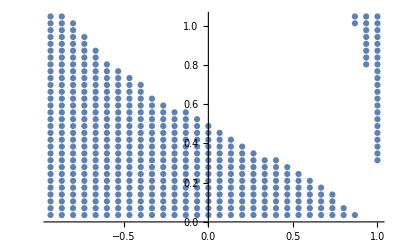

```mathematica
ListPlot[points1]
```

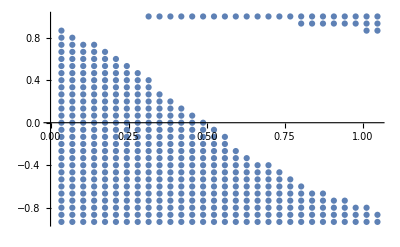

```mathematica
ListPlot[Table[{points1[[i]][[2]],points1[[i]][[1]]},{i,Length[points1]}]]
```